```mathematica
Sum[b^k/k!, {k, n+1, Infinity}]
```

(ⅇ^b (Gamma[1+n]-Gamma[1+n,b]))/Gamma[1+n]

```mathematica
D[Gamma[n+1, β], β]
```

-ⅇ^-β β^n

```mathematica
z[β_] := (m+1)/β^(m+1)E^β(Gamma[m+1] - Gamma[m+1, β])
```

```mathematica
FullSimplify[D[Log[z[β]], β]]
```

1-(1+m)/β+(ⅇ^-β β^m)/(Gamma[1+m]-Gamma[1+m,β])

```mathematica
n = 2;
f1[β_] := - (n+1)/β + 1 + (E^-β β^n)/(Gamma[n+1] - Gamma[n+1,β]);
f2[β_] := 1/n(E^-β β^(n+1) + (β - n) (Gamma[n+1] - Gamma[n+1,β]))/(β (Gamma[n] - Gamma[n,β]));
```

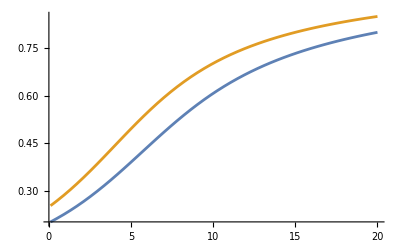

```mathematica
Plot[{f1[β], f2[β]}, {β, 0.1, 20}]
```

```mathematica
Limit[f1[β], β -> 0]
```

1/5

```mathematica
Limit[f2[β], β -> 0]
```

1/4

```mathematica
n Gamma[n, 1.0] + (1.0)^n Exp[-1.0]
```

1.8394

```mathematica
Gamma[n+1, 1.0]
```

1.8394

```mathematica
FullSimplify[
1/n(E^-β β^(n+1) + (β - n) (Gamma[n+1] - Gamma[n+1,β]))/(β (Gamma[n] - Gamma[n,β]))
== (E^-β β^n + (1 - n/β)(Gamma[n+1] - Gamma[n+1,β]))/(Gamma[n+1] - Gamma[n+1,β] + β^n E^-β),
Assumptions->{Element[n, Integers]}]
```

True

```mathematica
FullSimplify[
- (m+1)/β + 1 + (E^-β β^m)/(Gamma[m+1] - Gamma[m+1,β]) ==
1/m(E^-β β^(m+1) + (β - n) (Gamma[n+1] - Gamma[n+1,β]))/(β (Gamma[n] - Gamma[n,β]))
]
```